# Propiedad de umbrar y tren de picos en el modelo de Hodkin y Huxley

```mathematica
Cm=1; 
ENa=115;gNa=120;
EK=-12; gK=36;
EL=10.6;gL=0.3;
```

```mathematica
αn[u_] =(0.1-0.01 u)/(Exp[1-0.1 u]-1); βn[u_] = 0.125 Exp[-u/80];
τn[u_] = 1/(αn[u]+βn[u]);no[u_] = αn[u]/(αn[u]+βn[u]);
αm[u_] =(2.5-0.1 u)/(Exp[2.5-0.1 u]-1); βm[u_] = 4  Exp[-u/18];
τm[u_] = 1/(αm[u]+βm[u]);mo[u_] = αm[u]/(αm[u]+βm[u]);
αh[u_] =0.07 Exp[-u/20]; βh[u_] =1/  (Exp[3-0.1 u]+1);
τh[u_] = 1/(αh[u]+βh[u]);ho[u_] = αh[u]/(αh[u]+βh[u]);
```

```mathematica
J0[A_,t_,a_] :=A UnitBox[(t/a-1/2)]
```

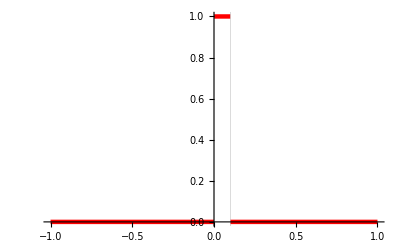

```mathematica
Plot[J0[1,t,.1],{t,-1,1},PlotStyle->{Thickness[.008],Red},GridLines->{{0,.1},None}]
```

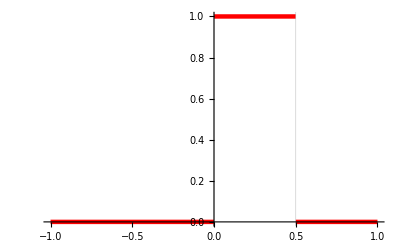

```mathematica
Plot[J0[1,t,.5],{t,-1,1},PlotStyle->{Thickness[.008],Red},GridLines->{{0,.5},None}]
```

-1/2<t/a-1/2 < 1/2 ⇒0<t/a< 1⇒0<t <a

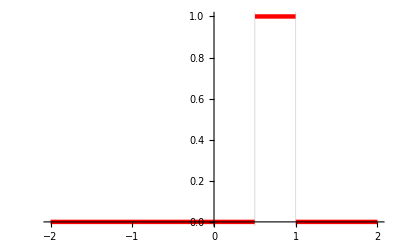

```mathematica
Plot[J0[1,t-.5,.5],{t,-2,2},PlotStyle->{Thickness[.008],Red},GridLines->{{.5,1},None}]
```

## Impulso corto al inicio

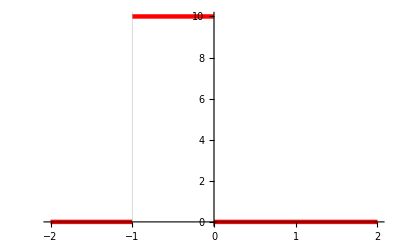

```mathematica
Plot[J0[10,t+1,1],{t,-2,2},PlotStyle->{Thickness[.008],Red},GridLines->{{-1,0},None}]
```

```mathematica
init={u[-10]==0,m[-10]==0,n[-10]==0,h[-10]==0}
```

{u[-10]==0,m[-10]==0,n[-10]==0,h[-10]==0}

```mathematica
HH0[A_]:={
Cm u'[t]== -gNa m[t]^3 h[t] (u[t]-ENa) -gK  n[t]^4  (u[t]-EK) - gL (u[t]-EL) +J0[A,t+1,1],
m'[t]==αm[u[t]] (1-m[t]) - βm[u[t]] m[t],
n'[t]==αn[u[t]] (1-n[t]) - βn[u[t]] n[t],
h'[t]==αh[u[t]] (1-h[t]) - βh[u[t]]h[t]}
```

```mathematica
tmax=50;
```

```mathematica
Manipulate[
sol1=NDSolve[Join[init,HH0[A]],{u[t],m[t],n[t] ,h[t]},{t,-10,tmax}]//Flatten;
Plot[Evaluate[{m[t],n[t],h[t]}/.sol1],{t,-10,tmax},PlotStyle->{ Blue, Green, Magenta},PlotLabel-> "Variables de compuerta. A = "<>ToString[A],PlotLegends->{"m","n","h"}, PlotRange-> All],{A,.1,70,.5}
]
```

```mathematica
Manipulate[
sol1=NDSolve[Join[init,HH0[A]],{u[t],m[t],n[t] ,h[t]},{t,-10,tmax}]//Flatten;
Plot[{J0[A,t+1,1],u[t]/.sol1},{t,-10,tmax},PlotStyle->{{Dashed,Blue},Red},PlotRange -> {-20,100},PlotLabel-> "Potencial transmembrana. A = "<>ToString[A],PlotLegends->{"u"},PlotRange-> All],{A,0,750,.5}
]
```

## Impulso corto a los 10 ms

```mathematica
HH1[A_]:={
Cm u'[t]== -gNa m[t]^3 h[t] (u[t]-ENa) -gK  n[t]^4  (u[t]-EK) - gL (u[t]-EL) +J0[A,t-10,1],
m'[t]==αm[u[t]] (1-m[t]) - βm[u[t]] m[t],
n'[t]==αn[u[t]] (1-n[t]) - βn[u[t]] n[t],
h'[t]==αh[u[t]] (1-h[t]) - βh[u[t]]h[t]}
```

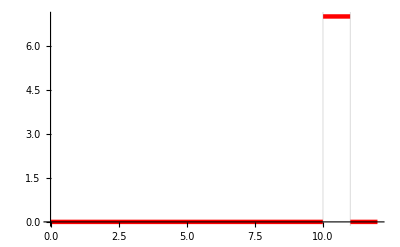

```mathematica
Plot[J0[7,t-10,1],{t,0,12},PlotStyle->{Thickness[.008],Red},GridLines->{{10,11},None}]
```

```mathematica
tmax=50
```

50

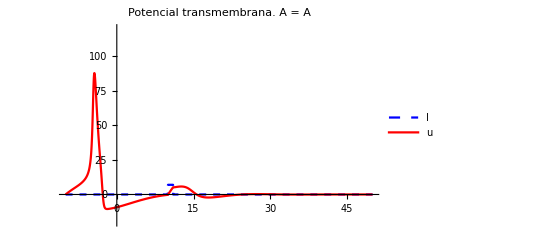

```mathematica
sol2=NDSolve[Join[init,HH1[6]],{u[t],m[t],n[t] ,h[t]},{t,-10,tmax}]//Flatten;
Plot[{J0[7,t-10,1],u[t]/.sol2},{t,-10,tmax},PlotStyle->{{Dashed,Blue},Red},PlotRange -> {-20,120},PlotLabel-> "Potencial transmembrana. A = "<>ToString[A],PlotLegends->{"I","u"},PlotRange-> All]
```

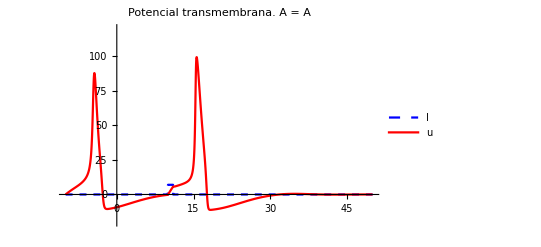

```mathematica
sol2=NDSolve[Join[init,HH1[6.5]],{u[t],m[t],n[t] ,h[t]},{t,-10,tmax}]//Flatten;
Plot[{J0[7,t-10,1],u[t]/.sol2},{t,-10,tmax},PlotStyle->{{Dashed,Blue},Red},PlotRange -> {-20,120},PlotLabel-> "Potencial transmembrana. A = "<>ToString[A],PlotLegends->{"I","u"},PlotRange-> All]
```

```mathematica
Manipulate[
sol2=NDSolve[Join[init,HH1[A]],{u[t],m[t],n[t] ,h[t]},{t,-10,tmax}]//Flatten;
Plot[{J0[7,t-10,1],u[t]/.sol2},{t,-10,tmax},PlotStyle->{{Dashed,Blue},Red},PlotRange -> {-20,120},PlotLabel-> "Potencial transmembrana. A = "<>ToString[A],PlotLegends->{"I","u"},PlotRange-> All],{A,0,75,.5}
]
```

NDSolve::deqn: Equation or list of equations expected instead of 
    Join[init, HH1[6.5]] in the first argument Join[init, HH1[6.5]].

Plot::plln: Limiting value tmax in {t, -10, tmax}
     is not a machine-sized real number.

## Impulso constante a los 10 ms

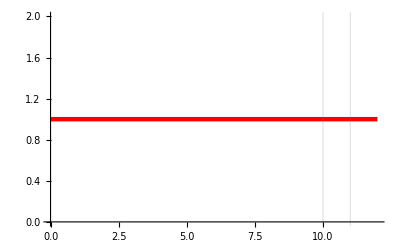

```mathematica
Plot[UnitStep[t],{t,0,12},PlotStyle->{Thickness[.008],Red},GridLines->{{10,11},None}]
```

```mathematica
HH2[A_]:={
Cm u'[t]== -gNa m[t]^3 h[t] (u[t]-ENa) -gK  n[t]^4  (u[t]-EK) - gL (u[t]-EL) +A UnitStep[t],
m'[t]==αm[u[t]] (1-m[t]) - βm[u[t]] m[t],
n'[t]==αn[u[t]] (1-n[t]) - βn[u[t]] n[t],
h'[t]==αh[u[t]] (1-h[t]) - βh[u[t]]h[t]}
```

```mathematica
tmax=50
```

50

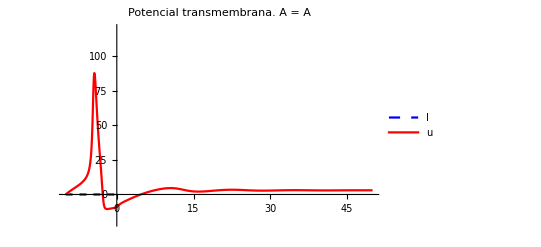

```mathematica
sol1=NDSolve[Join[init,HH2[4.5]],{u[t],m[t],n[t] ,h[t]},{t,-10,tmax}]//Flatten;
Plot[{A UnitStep[t],u[t]/.sol1},{t,-10,tmax},PlotStyle->{{Dashed,Blue},Red},PlotRange -> {-20,120},PlotLabel-> "Potencial transmembrana. A = "<>ToString[A],PlotLegends->{"I","u"},PlotRange-> All]
```

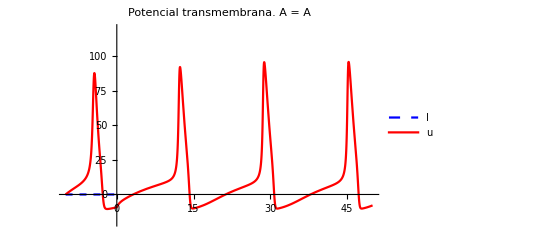

```mathematica
sol1=NDSolve[Join[init,HH2[7.5]],{u[t],m[t],n[t] ,h[t]},{t,-10,tmax}]//Flatten;
Plot[{A UnitStep[t],u[t]/.sol1},{t,-10,tmax},PlotStyle->{{Dashed,Blue},Red},PlotRange -> {-20,120},PlotLabel-> "Potencial transmembrana. A = "<>ToString[A],PlotLegends->{"I","u"},PlotRange-> All]
```

```mathematica
Manipulate[
sol1=NDSolve[Join[init,HH2[A]],{u[t],m[t],n[t] ,h[t]},{t,-10,tmax}]//Flatten;
Plot[{A UnitStep[t],u[t]/.sol1},{t,-10,tmax},PlotStyle->{{Dashed,Blue},Red},PlotRange -> {-20,120},PlotLabel-> "Potencial transmembrana. A = "<>ToString[A],PlotLegends->{"I","u"},PlotRange-> All],{A,0,75,.5}
]
```

NDSolve::deqn: Equation or list of equations expected instead of 
    Join[init, HH2[7.5]] in the first argument Join[init, HH2[7.5]].

Plot::plln: Limiting value tmax in {t, -10, tmax}
     is not a machine-sized real number.

## Lectura complementarias

https://neuronaldynamics.epfl.ch/

Libro electrónico:
Neuronal Dynamics online book
From single neurons to networks and models of cognition

-Graphics-